# Bifurcation Diagrams

```mathematica
{α,β,σ,n,κ,δ}=.;
Gp[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β (1/n+(n-1)/n y)]))-κ;
Gn[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β ((n-1)/n y)]));


dydt[y_,Y_,α_,β_,σ_,nC_,nD_,κ_,δ_]=y(1-y)(1-Y)(Gp[y,α,β,σ,nC,κ] -Gn[y,α,β,σ,nD,κ]);
dYdt[y_,Y_,α_,β_,σ_,nC_,nD_,κ_,δ_]=-Y(δ-(1-Y)(Gp[y,α,β,σ,nC,κ] y+Gn[y,α,β,σ,nD,κ](1-y)));

Y[y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]:=1-δ/(Gp[y0,α,β,σ,nC,κ] y0+Gn[y0,α,β,σ,nD,κ](1-y0));
J[y0_,Y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]=D[{dydt[y0,Y0,α,β,σ,nC,nD,κ,δ],dYdt[y0,Y0,α,β,σ,nC,nD,κ,δ]},{{y0,Y0}}];
stableQ1[y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]:=(Tr[#]<0&&Det[#]>0)&@J[y0,Y[y0,α,β,σ,nC,nD,κ,δ],α,β,σ,nC,nD,κ,δ];
```

```mathematica
Vary neighborhood size
```

### n_D=50;

neighborhood size Vary

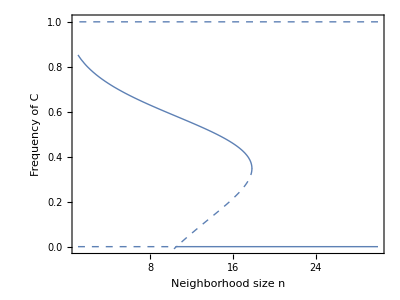

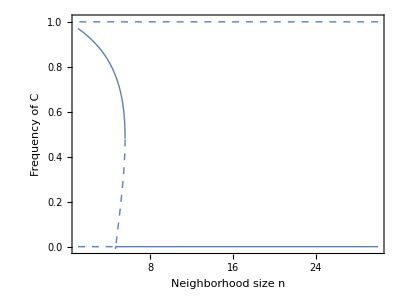

```mathematica
{α,β,σ,n,κ,δ}=.;
{α,β,σ,κ,δ,nD}={1,5,2,0.5,0.9,50};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,nD,κ,δ],α,β,σ,n,nD,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,nD,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Frequency of C"}
,PlotPoints->50
],
ContourPlot[dydt[y,Y[y,α,β,σ,n,nD,κ,δ],α,β,σ,n,nD,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,nD,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Frequency of C"}
,PlotPoints->50]
]
{α,β,σ,κ,δ}={1,2,3,0.5,0.9};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,nD,κ,δ],α,β,σ,n,nD,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,nD,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Frequency of C"}
,PlotPoints->50
],

ContourPlot[dydt[y,Y[y,α,β,σ,n,nD,κ,δ],α,β,σ,n,nD,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,nD,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Frequency of C"}
,PlotPoints->50]
]
```

### n_D=5;

neighborhood size Vary

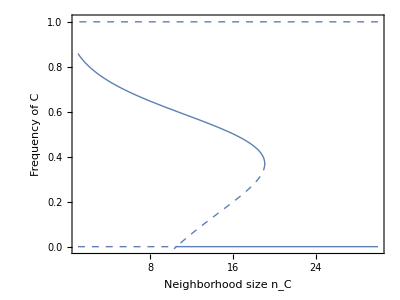

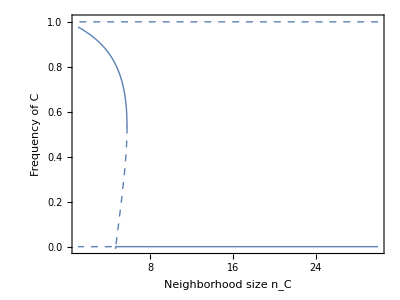

```mathematica
{α,β,σ,n,κ,δ}=.;
{α,β,σ,κ,δ,nD}={1,5,2,0.5,0.9,25};
Gp[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β (1/n+(n-1)/n y)]))-κ;
Gn[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β ((n-1)/n y)]));


dydt[y_,Y_,α_,β_,σ_,nC_,nD_,κ_,δ_]=y(1-y)(1-Y)(Gp[y,α,β,σ,nC,κ] -Gn[y,α,β,σ,nD,κ]);
dYdt[y_,Y_,α_,β_,σ_,nC_,nD_,κ_,δ_]=-Y(δ-(1-Y)(Gp[y,α,β,σ,nC,κ] y+Gn[y,α,β,σ,nD,κ](1-y)));

Y[y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]:=1-δ/(Gp[y0,α,β,σ,nC,κ] y0+Gn[y0,α,β,σ,nD,κ](1-y0));
J[y0_,Y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]=D[{dydt[y0,Y0,α,β,σ,nC,nD,κ,δ],dYdt[y0,Y0,α,β,σ,nC,nD,κ,δ]},{{y0,Y0}}];
stableQ1[y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]:=(Tr[#]<0&&Det[#]>0)&@J[y0,Y[y0,α,β,σ,nC,nD,κ,δ],α,β,σ,nC,nD,κ,δ];


Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,nD,κ,δ],α,β,σ,n,nD,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,nD,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n_C","Frequency of C"}
,PlotPoints->50
],
ContourPlot[dydt[y,Y[y,α,β,σ,n,nD,κ,δ],α,β,σ,n,nD,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,nD,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n_C","Frequency of C"}
,PlotPoints->50]
]


{α,β,σ,κ,δ}={1,2,3,0.5,0.1};
Gp[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β (1/n+(n-1)/n y)]))-κ;
Gn[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β ((n-1)/n y)]));


dydt[y_,Y_,α_,β_,σ_,nC_,nD_,κ_,δ_]=y(1-y)(1-Y)(Gp[y,α,β,σ,nC,κ] -Gn[y,α,β,σ,nD,κ]);
dYdt[y_,Y_,α_,β_,σ_,nC_,nD_,κ_,δ_]=-Y(δ-(1-Y)(Gp[y,α,β,σ,nC,κ] y+Gn[y,α,β,σ,nD,κ](1-y)));

Y[y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]:=1-δ/(Gp[y0,α,β,σ,nC,κ] y0+Gn[y0,α,β,σ,nD,κ](1-y0));
J[y0_,Y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]=D[{dydt[y0,Y0,α,β,σ,nC,nD,κ,δ],dYdt[y0,Y0,α,β,σ,nC,nD,κ,δ]},{{y0,Y0}}];
stableQ1[y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]:=(Tr[#]<0&&Det[#]>0)&@J[y0,Y[y0,α,β,σ,nC,nD,κ,δ],α,β,σ,nC,nD,κ,δ];
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,nD,κ,δ],α,β,σ,n,nD,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,nD,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n_C","Frequency of C"}
,PlotPoints->50
],

ContourPlot[dydt[y,Y[y,α,β,σ,n,nD,κ,δ],α,β,σ,n,nD,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,nD,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n_C","Frequency of C"}
,PlotPoints->50]
]
```

### n_D=n_C+Δn;

neighborhood size Vary

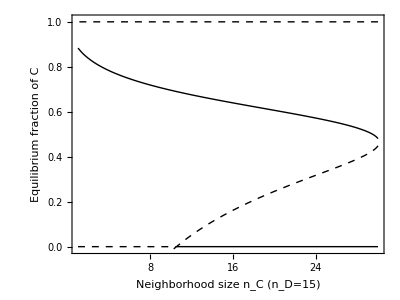

```mathematica
{α,β,σ,n,κ,δ}=.;
{α,β,σ,κ,δ}={1,5,2,0.5,0.1};
Gp[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β (1/n+(n-1)/n y)]))-κ;
Gn[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β ((n-1)/n y)]));


dydt[y_,Y_,α_,β_,σ_,nC_,nD_,κ_,δ_]=y(1-y)(1-Y)(Gp[y,α,β,σ,nC,κ] -Gn[y,α,β,σ,nD,κ]);
dYdt[y_,Y_,α_,β_,σ_,nC_,nD_,κ_,δ_]=-Y(δ-(1-Y)(Gp[y,α,β,σ,nC,κ] y+Gn[y,α,β,σ,nD,κ](1-y)));

Y[y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]:=1-δ/(Gp[y0,α,β,σ,nC,κ] y0+Gn[y0,α,β,σ,nD,κ](1-y0));
J[y0_,Y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]=D[{dydt[y0,Y0,α,β,σ,nC,nD,κ,δ],dYdt[y0,Y0,α,β,σ,nC,nD,κ,δ]},{{y0,Y0}}];
stableQ1[y0_,α_,β_,σ_,nC_,nD_,κ_,δ_]:=(Tr[#]<0&&Det[#]>0)&@J[y0,Y[y0,α,β,σ,nC,nD,κ,δ],α,β,σ,nC,nD,κ,δ];

Δ=15;
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,n+Δ,κ,δ],α,β,σ,n,Δ,κ,δ]==0
,{n,Max[1,1-Δ],30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,Δ,κ,δ]]
,ContourStyle-> {Thick,Dashed,Black}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n_C (n_D="<>ToString[Δ]<>")","Equilibrium fraction of C"}
,PlotPoints->50
],
ContourPlot[dydt[y,Y[y,α,β,σ,n,n+Δ,κ,δ],α,β,σ,n,Δ,κ,δ]==0
,{n,Max[1,1-Δ],30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,Δ,κ,δ]]
,ContourStyle-> {Thick,Black}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
(*,FrameLabel->{"Neighborhood size n_C (n_D="<>ToString[Δ]<>")","Frequency of C"}*)
,PlotPoints->50]
]
```

## Vary benefit parameter

```mathematica
{α,β,σ,n,κ,δ}=.;
{α,σ,n,κ,δ}={1,2,25,0.5,0.1};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
,
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
]
{α,σ,n,κ,δ}={1,3,25,0.5,0.1};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
,
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
]
```

-Graphics-

-Graphics-

```mathematica
{dydt[y0,Y0,α,β,σ,n,κ,δ],dYdt[y0,Y0,α,β,σ,n,κ,δ]}
```

{dydt[y0,Y0,1,β,3,25,0.5,0.1],dYdt[y0,Y0,1,β,3,25,0.5,0.1]}

```mathematica
Solve[δ-(1-Y0) (((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+y0 (((1+ⅇ^σ) α)/(1+ⅇ^(-(1/n+((-1+n) y0)/n) β+σ))-κ))==0,Y0]
```

{{Y0→(-0.1+1. ((21.0855 (1.-1. y0))/(1.+ⅇ^(3-(24 y0 β)/25))+(-0.5+21.0855/(1.+ⅇ^(3+(-1/25-(24 y0)/25) β))) y0))/((21.0855 (1.-1. y0))/(1.+ⅇ^(3-(24 y0 β)/25))+(-0.5+21.0855/(1.+ⅇ^(3+(-1/25-(24 y0)/25) β))) y0)}}